```mathematica
SusceptHeight={{4,1.60186,0.0023}, {8,5.147281442,0.0177},{16,17.131, 0.1384}, {32, 56.5890561,1.0271},{64,185.373008,7.5628}};
SusceptHeightPoints = Table[Log[{SusceptHeight[[i]][[1]],SusceptHeight[[i]][[2]]}], {i, 1, Length[SusceptHeight]}];
SusceptHeightErrors = Table[SusceptHeight[[i]][[3]]/SusceptHeight[[i]][[2]],{i,1,Length[SusceptHeight]}];
SusceptWidth={{4, 0.16554,0.00115}, {8,0.08934, 0.00100}, {16,0.05108,0.000880},{32, 0.027687,0.000965},{64,0.01433,0.000868}};
SusceptWidthPoints = Table[Log[{SusceptWidth[[i]][[1]],SusceptWidth[[i]][[2]]}], {i, 1, Length[SusceptWidth]}];
SusceptWidthErrors = Table[SusceptWidth[[i]][[3]]/SusceptWidth[[i]][[2]],{i,1,Length[SusceptWidth]}];
SusceptPos={{4, 0.528509800144,0.00043}, {8, 0.6423461, 0.000488}, {16,0.69354,0.0005567},{32, 0.71767, 0.000657},{64,0.72953,0.000701}};
SusceptPosPoints = Table[{SusceptPos[[i]][[1]],SusceptPos[[i]][[2]]}, {i, 1, Length[SusceptPos]}];
SusceptPosErrors = Table[SusceptPos[[i]][[3]],{i,1,Length[SusceptPos]}];
Needs["ErrorBarPlots`"]
```

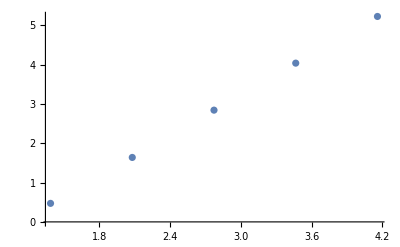

```mathematica
ListPlot[SusceptHeightPoints]
```

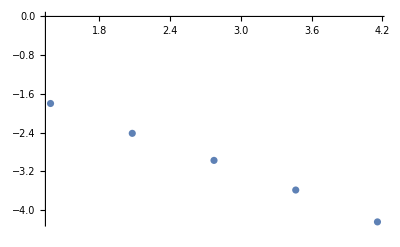

```mathematica
ListPlot[SusceptWidthPoints]
```

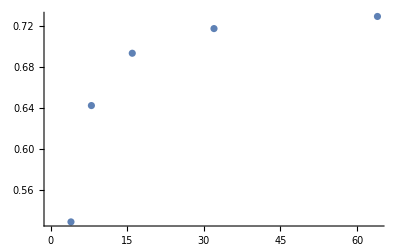

```mathematica
ListPlot[SusceptPosPoints]
```

```mathematica
SusceptHeightFit = NonlinearModelFit[SusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SusceptHeightErrors^2];
```

```mathematica
SusceptHeightFit[{"BestFit","ParameterTable"}]
```

{-1.88601+1.69962 x, | Estimate | Standard Error | t-Statistic | P-Value
sigmav | 1.69962 | 0.00838777 | 202.631 | 2.65042×10^-7
b | -1.88601 | 0.0132218 | -142.644 | 7.59683×10^-7}

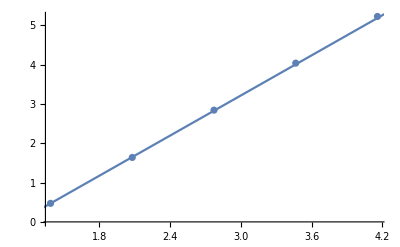

```mathematica
Show[
ErrorListPlot[
Table[{SusceptHeightPoints[[i]][[1]],SusceptHeightPoints[[i]][[2]], SusceptHeightErrors[[i]]},{i,1,Length[SusceptHeightPoints]}]],
Plot[SusceptHeightFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptWidthFit = NonlinearModelFit[SusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SusceptWidthErrors^2];
```

```mathematica
SusceptWidthFit[{"BestFit","ParameterTable"}]
```

{-0.604359-0.863273 x, | Estimate | Standard Error | t-Statistic | P-Value
v | 1.15838 | 0.0160445 | 72.1982 | 5.85587×10^-6
b | -0.604359 | 0.0222488 | -27.1637 | 0.000109493}

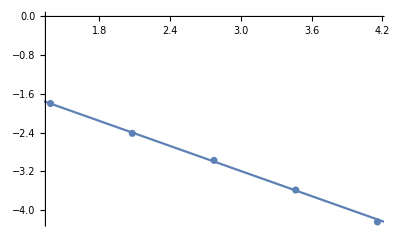

```mathematica
Show[
ErrorListPlot[Table[{SusceptWidthPoints[[i]][[1]],SusceptWidthPoints[[i]][[2]], SusceptWidthErrors[[i]]},{i,1,Length[SusceptWidthPoints]}]],
Plot[SusceptWidthFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptPosFit = NonlinearModelFit[SusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SusceptPosErrors^2];
```

```mathematica
SusceptPosFit[{"BestFit","ParameterTable"}]
```

{0.738271-0.994618/x^1.12291, | Estimate | Standard Error | t-Statistic | P-Value
A | -0.994618 | 0.0149283 | -66.6265 | 0.000225195
v | 1.12291 | 0.0127816 | 87.8537 | 0.000129538
b | 0.738271 | 0.000888961 | 830.488 | 1.44988×10^-6}

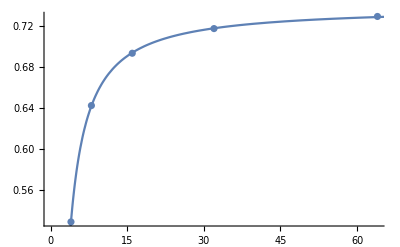

```mathematica
Show[
ErrorListPlot[Table[{SusceptPosPoints[[i]][[1]],SusceptPosPoints[[i]][[2]], SusceptPosErrors[[i]]},{i,1,Length[SusceptPosPoints]}]],
Plot[SusceptPosFit[x],{x,0.1,150},PlotRange->Full]
]
```

```mathematica
MagnetizationHeight = {{8, 0.90404375}, {16,0.841697265625}, {32,0.774832519531}, {64,0.711084960937}, {128, 0.659222839355}};
```

```mathematica
ListPlot[Log[MagnetizationHeight]]
```

ListPlot::lpn: Log[MagnetizationHeight] is not a list of numbers or pairs of numbers.

ListPlot[Log[MagnetizationHeight]]

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{0.142935-0.115453 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | 0.115453 | 0.00197076 | 58.5831 | 0.0000109572
b | 0.142935 | 0.00709809 | 20.1371 | 0.000267694}

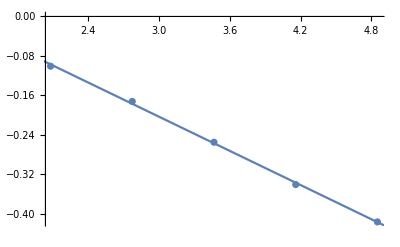

```mathematica
Show[ListPlot[Log[MagnetizationHeight]],Plot[MagnetizationHeightFit[x],{x,0,5}]]
```

```mathematica
MagnetizationHeight = {{8,0.02368}, {16,0.040963}, {32,0.48735}, {64,0.553383}};
```

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{-7.43093+1.72122 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | -1.72122 | 0.446808 | -3.85225 | 0.0612592
b | -7.43093 | 1.43604 | -5.17461 | 0.0353762}

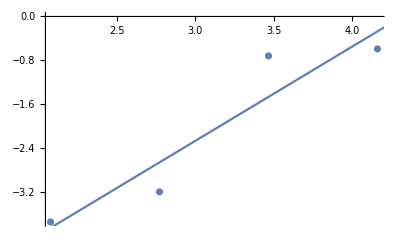

```mathematica
Show[ListPlot[Log[MagnetizationHeight],PlotRange->Full],Plot[MagnetizationHeightFit[x],{x,0,5},PlotRange->Full]]
```

```mathematica
SusceptWidthPoints//N
```

{{1.38629,-1.79854},{2.07944,-2.41531},{2.77259,-2.97436},{3.46574,-3.58679},{4.15888,-4.2454}}